```mathematica
texlis=ImageResize[ExampleData[{"ColorTexture",#},"Image"],{50,50}]&/@ExampleData["ColorTexture"][[All,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
walls={
Gray,Cuboid[{100+21+1,100-100+1,-10},{100+1+19,100-60+1,10}],
Gray,Cuboid[{100+1+19,100-60+1,10},{100+1+40,100-62+1,-10}],
Gray,Cuboid[{100+1+38,100-62+1,-10},{100+1+40,100-22+1,10}],
Gray,Cuboid[{100+1+38,100-22+1,-10},{100+1+70,100-24+1,10}],
Gray,Cuboid[{100+1+70,100-22+1,10},{100+1+68,100-78+1,-10}],
Gray,Cuboid[{100+1+70,100-78+1,-10},{100+1+44,100-76+1,10}],
Gray,Cuboid[{100-60+1,100+0+1,-10},{100+1+40,100+2+1,10}],
Gray,Cuboid[{100-19+1,100-100+1,-10},{100-21+1,100-75+1,10}],
Gray,Cuboid[{100-19+1,100-77+1,10},{100-65+1,100-75+1,-10}],
Gray,Cuboid[{100-100+1,100-25+1,10},{100-55+1,100-27+1,-10}],
Gray,Cuboid[{100+45+1,100+100,10},{100+47+1,100+50+1,-10}],
Gray,Cuboid[{100+45+1,100+52+1,10},{100+65+1,100+50+1,-10}],
Gray,Cuboid[{100+65+1,100+68+1,10},{100+100,100+70+1,-10}],
Gray,Cuboid[{100-30+1,100+100,10},{100-32+1,100+40+1,-10}],
Gray,Cuboid[{100-30+1,100+40+1,10},{100-68+1,100+42+1,-10}],
Gray,Cuboid[{100-68+1,100+40+1,10},{100-66+1,100+70+1,-10}]
};
walledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]]~Join~
{{200,∞},{1,200},{-∞,1},{1,200},{1,200},{200,∞},{1,200},{-∞,1}};
cutwalledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]];
wal1=Range[#⟦1⟧,#⟦2⟧]&/@cutwalledges;
wallcoords=Flatten[Table[{wal1⟦i,j⟧,wal1⟦i+1,k⟧},{i,1,Length@wal1,2},{j,Length@wal1⟦i⟧},{k,Length@wal1⟦i+1⟧}],2];
Do[wallcoords⟦i⟧=(wallcoords⟦i,1⟧-1)*200+wallcoords⟦i,2⟧,{i,Length@wallcoords}];
n=200;
gridg=GridGraph[{n,n}];
gridg=VertexDelete[gridg,DeleteDuplicates@wallcoords];

gctoxyc[x_]:=If[Mod[x,200]==0,{Quotient[x,200],200},{Quotient[x,200]+1,Mod[x,200]}];
rotatevec[vec_,ang_]:=Module[
{x,y,z,newx,newy},
{x,y,z}=vec⟦2⟧;
newx=x*Cos@ang-y*Sin@ang;
newy=y*Cos@ang+x*Sin@ang;
{vec⟦1⟧,{newx,newy,z}}
];
```

```mathematica
DynamicModule[
{
px=100,
py=10,
pz=0,
viewd=0,
rb=0,
viewvector,
walls,
walledges,
fi,
checkbonds,
n=200,
wallcoords,
wal1,
gctoxyc,
botx=10,
boty=180,
botz=-10,
cutwalledges,
kudagolist={},
myshortestpath,
i=1
},
viewvector=Dynamic@{{px,py-1,pz},{px+viewd,py+rb,pz}};
walls={
Gray,Cuboid[{100+21+1,100-100+1,-10},{100+1+19,100-60+1,10}],
Gray,Cuboid[{100+1+19,100-60+1,10},{100+1+40,100-62+1,-10}],
Gray,Cuboid[{100+1+38,100-62+1,-10},{100+1+40,100-22+1,10}],
Gray,Cuboid[{100+1+38,100-22+1,-10},{100+1+70,100-24+1,10}],
Gray,Cuboid[{100+1+70,100-22+1,10},{100+1+68,100-78+1,-10}],
Gray,Cuboid[{100+1+70,100-78+1,-10},{100+1+44,100-76+1,10}],
Gray,Cuboid[{100-60+1,100+0+1,-10},{100+1+40,100+2+1,10}],
Gray,Cuboid[{100-19+1,100-100+1,-10},{100-21+1,100-75+1,10}],
Gray,Cuboid[{100-19+1,100-77+1,10},{100-65+1,100-75+1,-10}],
Gray,Cuboid[{100-100+1,100-25+1,10},{100-55+1,100-27+1,-10}],
Gray,Cuboid[{100+45+1,100+100,10},{100+47+1,100+50+1,-10}],
Gray,Cuboid[{100+45+1,100+52+1,10},{100+65+1,100+50+1,-10}],
Gray,Cuboid[{100+65+1,100+68+1,10},{100+100,100+70+1,-10}],
Gray,Cuboid[{100-30+1,100+100,10},{100-32+1,100+40+1,-10}],
Gray,Cuboid[{100-30+1,100+40+1,10},{100-68+1,100+42+1,-10}],
Gray,Cuboid[{100-68+1,100+40+1,10},{100-66+1,100+70+1,-10}]
};

walledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]]
~Join~
{{199,∞},{1,200},{-∞,2},{1,200},{1,200},{199,∞},{1,200},{-∞,2}}
~Join~
{{100,100+5},{100,100+5}};

cutwalledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]];

gctoxyc[x_]:=If[Mod[x,200]==0,{Quotient[x,200],200},{Quotient[x,200]+1,Mod[x,200]}];

myshortestpath[px_,py_,botx_,boty_]:=Module[
{gcord,gcordbot},
gcord=(px-1)*200+py;
gcordbot=(botx-1)*200+boty;
kudagolist=FindShortestPath[gridg,gcord,gcordbot];
gctoxyc/@kudagolist
];

checkbonds[{x_,y_,z_}]:=Module[
{},
Total[
Table[
Boole[
If[
fi[x,y,walledges⟦i⟧,walledges⟦i+1⟧],
True,
False
]
],
{i,1,Length@walledges,2}
]
]
];

fi[x_,y_,xpat_,ypat_]:=Between[x,xpat]&&Between[y,ypat];
EventHandler[
Column[
{
Show[
Graphics3D[
walls
],
Graphics3D[
{Green,Dynamic@Cuboid[{px,py,10},{px+2,py+2,11}]}
],
Graphics3D[
{
Red,
Dynamic@Cuboid[{botx,boty,botz},{botx+3,boty+2,botz+15}],
Black,
Dynamic@Cuboid[{botx,boty,botz+10},{botx+1,boty+2,botz+12}],
Black,
Dynamic@Cuboid[{botx+2,boty,botz+10},{botx+3,boty+2,botz+12}],
Black,
Dynamic@Cuboid[{botx,boty,botz+6},{botx+3,boty+2,botz+8}],
Red,
Dynamic@Cuboid[{botx,boty,10},{botx+3,boty+2,11}]
}
],
      ContourPlot3D[
{
z==-10,
z==10
},
{x,1,200},
{y,1,200},
{z,-10,10},
ContourStyle->
{
Texture@ExampleData[{"ColorTexture","LightCherry"}],
Texture@ExampleData[{"ColorTexture","LightCherry"}]
},
Mesh->False
],
 ContourPlot3D[
{
y==200,
y==1,
x==200,
x==1
},
{x,1,200},
{y,1,200},
{z,-10,10},
ContourStyle->
{
Hue[0.58,0.72,0.42],
Hue[0.58,0.72,0.42],
Hue[0.58,0.72,0.42],
Hue[0.58,0.72,0.42]
},
Mesh->False
],
ViewAngle->π/2,
ViewVector->viewvector,
ImageSize->550
],
Dynamic@
Refresh[
If[
i≤Length@myshortestpath[botx,boty,px,py]-1,
{botx,boty}=Most[myshortestpath[botx,boty,px,py]]⟦i++⟧,
i=1;
{botx,boty}=Most[myshortestpath[botx,boty,px,py]]⟦i++⟧
],
TrackedSymbols:>{},
UpdateInterval->1
]
},
ItemStyle->White
],
DynamicUpdating->True,
{
"DownArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧-{0,2,0}]==0&&checkbonds[viewvector⟦1,1⟧-{0,2,0}]==0,py-=2]),
"UpArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧+{0,2,0}]==0&&checkbonds[viewvector⟦1,1⟧+{0,2,0}]==0,py+=2]),
"RightArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧+{2,0,0}]==0&&checkbonds[viewvector⟦1,1⟧+{2,0,0}]==0,px+=2]),
"LeftArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧-{2,0,0}]==0&&checkbonds[viewvector⟦1,1⟧-{2,0,0}]==0,px-=2]),
{"KeyDown","w"}:>(rb=0),
{"KeyDown","s"}:>(rb=-2),
{"KeyDown","a"}:>(viewd-=2),
{"KeyDown","d"}:>(viewd+=2)
}
]
]
```

```mathematica
walls={
Gray,Cuboid[{100+21+1,100-100+1,-10},{100+1+19,100-60+1,10}],Gray,Cuboid[{100+1+19,100-60+1,10},{100+1+40,100-62+1,-10}],Gray,Cuboid[{100+1+38,100-62+1,-10},{100+1+40,100-22+1,10}],Gray,Cuboid[{100+1+38,100-22+1,-10},{100+1+70,100-24+1,10}],Gray,Cuboid[{100+1+70,100-22+1,10},{100+1+68,100-78+1,-10}],Gray,Cuboid[{100+1+70,100-78+1,-10},{100+1+44,100-76+1,10}],Gray,Cuboid[{100-60+1,100+0+1,-10},{100+1+40,100+2+1,10}],Gray,Cuboid[{100-19+1,100-100+1,-10},{100-21+1,100-75+1,10}],Gray,Cuboid[{100-19+1,100-77+1,10},{100-65+1,100-75+1,-10}],Gray,Cuboid[{100-100+1,100-25+1,10},{100-55+1,100-27+1,-10}],Gray,Cuboid[{100+45+1,100+100,10},{100+47+1,100+50+1,-10}],Gray,Cuboid[{100+45+1,100+52+1,10},{100+65+1,100+50+1,-10}],Gray,Cuboid[{100+65+1,100+68+1,10},{100+100,100+70+1,-10}],Gray,Cuboid[{100-30+1,100+100,10},{100-32+1,100+40+1,-10}],Gray,Cuboid[{100-30+1,100+40+1,10},{100-68+1,100+42+1,-10}],Gray,Cuboid[{100-68+1,100+40+1,10},{100-66+1,100+70+1,-10}]
};
walledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls[[2;; ;;2]]],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls[[2;; ;;2]]],2]];

wal1=Range[#⟦1⟧,#⟦2⟧]&/@walledges;

wallcoords=Flatten[Table[{wal1⟦i,j⟧,wal1⟦i+1,k⟧},{i,1,Length@wal1,2},{j,Length@wal1⟦i⟧},{k,Length@wal1⟦i+1⟧}],2];
Do[wallcoords⟦i⟧=(wallcoords⟦i,1⟧-1)*200+wallcoords⟦i,2⟧,{i,Length@wallcoords}];
Length@Sort@wallcoords
Length@DeleteDuplicates@Sort@wallcoords
n=200;
gridg=GridGraph[{n,n}];
(*graphmap=VertexDelete[gridg,#]&/@wallcoords;*)
VertexList@gridg;
```

2031

1950

```mathematica
gridg=VertexDelete[gridg,Sort@DeleteDuplicates@wallcoords];
```

```mathematica
botx=100
boty=198
botz=-10
(100-1)*200+198
(100-1)*200+10
```

100

198

-10

19998

19810

```mathematica
ExampleData[{"ColorTexture","LightCherry"}]
```

-Graphics-

```mathematica
sh=FindShortestPath[gridg,19998,19810]
```

{19998,19997,19996,19995,19994,19993,19992,19991,19990,19989,19988,19987,19986,19985,19984,19983,19982,19981,19980,19979,19978,19977,19976,19975,19974,19973,19972,19971,19970,19969,19968,19967,19966,19965,19964,19963,19962,19961,19960,19959,19958,19957,19956,19955,19954,19953,19952,19951,19950,19949,19948,19947,19946,19945,19944,19943,19942,19941,19940,19939,19938,19937,19936,19935,19934,19933,19932,19931,19930,19929,19928,19927,19926,19925,19924,19923,19922,19921,19920,19919,19918,19917,19916,19915,19914,19913,19912,19911,19910,19909,19908,19907,19906,19905,19904,20104,20304,20504,20704,20904,21104,21304,21504,21704,21904,22104,22304,22504,22704,22904,23104,23304,23504,23704,23904,24104,24304,24504,24704,24904,25104,25304,25504,25704,25904,26104,26304,26504,26704,26904,27104,27304,27504,27704,27904,28104,28304,28303,28302,28301,28300,28100,27900,27700,27500,27300,27100,26900,26700,26500,26300,26100,25900,25700,25500,25300,25100,24900,24700,24500,24300,24100,23900,23700,23500,23300,23100,22900,22700,22500,22300,22100,21900,21700,21500,21300,21100,20900,20700,20500,20300,20100,19900,19899,19898,19897,19896,19895,19894,19893,19892,19891,19890,19889,19888,19887,19886,19885,19884,19883,19882,19881,19880,19879,19878,19877,19876,19875,19874,19873,19872,19871,19870,19869,19868,19867,19866,19865,19864,19863,19862,19861,19860,19859,19858,19857,19856,19855,19854,19853,19852,19851,19850,19849,19848,19847,19846,19845,19844,19843,19842,19841,19840,19839,19838,19837,19836,19835,19834,19833,19832,19831,19830,19829,19828,19827,19826,19825,19824,19823,19822,19821,19820,19819,19818,19817,19816,19815,19814,19813,19812,19811,19810}

```mathematica
If[Mod[#,200]==0,{Quotient[#,200],200},{Quotient[#,200]+1,Mod[#,200]}]&/@sh
```

{{100,198},{100,197},{100,196},{100,195},{100,194},{100,193},{100,192},{100,191},{100,190},{100,189},{100,188},{100,187},{100,186},{100,185},{100,184},{100,183},{100,182},{100,181},{100,180},{100,179},{100,178},{100,177},{100,176},{100,175},{100,174},{100,173},{100,172},{100,171},{100,170},{100,169},{100,168},{100,167},{100,166},{100,165},{100,164},{100,163},{100,162},{100,161},{100,160},{100,159},{100,158},{100,157},{100,156},{100,155},{100,154},{100,153},{100,152},{100,151},{100,150},{100,149},{100,148},{100,147},{100,146},{100,145},{100,144},{100,143},{100,142},{100,141},{100,140},{100,139},{100,138},{100,137},{100,136},{100,135},{100,134},{100,133},{100,132},{100,131},{100,130},{100,129},{100,128},{100,127},{100,126},{100,125},{100,124},{100,123},{100,122},{100,121},{100,120},{100,119},{100,118},{100,117},{100,116},{100,115},{100,114},{100,113},{100,112},{100,111},{100,110},{100,109},{100,108},{100,107},{100,106},{100,105},{100,104},{101,104},{102,104},{103,104},{104,104},{105,104},{106,104},{107,104},{108,104},{109,104},{110,104},{111,104},{112,104},{113,104},{114,104},{115,104},{116,104},{117,104},{118,104},{119,104},{120,104},{121,104},{122,104},{123,104},{124,104},{125,104},{126,104},{127,104},{128,104},{129,104},{130,104},{131,104},{132,104},{133,104},{134,104},{135,104},{136,104},{137,104},{138,104},{139,104},{140,104},{141,104},{142,104},{142,103},{142,102},{142,101},{142,100},{141,100},{140,100},{139,100},{138,100},{137,100},{136,100},{135,100},{134,100},{133,100},{132,100},{131,100},{130,100},{129,100},{128,100},{127,100},{126,100},{125,100},{124,100},{123,100},{122,100},{121,100},{120,100},{119,100},{118,100},{117,100},{116,100},{115,100},{114,100},{113,100},{112,100},{111,100},{110,100},{109,100},{108,100},{107,100},{106,100},{105,100},{104,100},{103,100},{102,100},{101,100},{100,100},{100,99},{100,98},{100,97},{100,96},{100,95},{100,94},{100,93},{100,92},{100,91},{100,90},{100,89},{100,88},{100,87},{100,86},{100,85},{100,84},{100,83},{100,82},{100,81},{100,80},{100,79},{100,78},{100,77},{100,76},{100,75},{100,74},{100,73},{100,72},{100,71},{100,70},{100,69},{100,68},{100,67},{100,66},{100,65},{100,64},{100,63},{100,62},{100,61},{100,60},{100,59},{100,58},{100,57},{100,56},{100,55},{100,54},{100,53},{100,52},{100,51},{100,50},{100,49},{100,48},{100,47},{100,46},{100,45},{100,44},{100,43},{100,42},{100,41},{100,40},{100,39},{100,38},{100,37},{100,36},{100,35},{100,34},{100,33},{100,32},{100,31},{100,30},{100,29},{100,28},{100,27},{100,26},{100,25},{100,24},{100,23},{100,22},{100,21},{100,20},{100,19},{100,18},{100,17},{100,16},{100,15},{100,14},{100,13},{100,12},{100,11},{100,10}}

```mathematica
{200,0}
```

{200,0}

```mathematica
(200-1)*200+1
```

39801

```mathematica
VertexList@gridg
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,37906,39926,39927,39928,39929,39930,39931,39932,39933,39934,39935,39936,39937,39938,39939,39940,39941,39942,39943,39944,39945,39946,39947,39948,39949,39950,39951,39952,39953,39954,39955,39956,39957,39958,39959,39960,39961,39962,39963,39964,39965,39966,39967,39968,39972,39973,39974,39975,39976,39977,39978,39979,39980,39981,39982,39983,39984,39985,39986,39987,39988,39989,39990,39991,39992,39993,39994,39995,39996,39997,39998,39999,40000}
 |  |  |  |

```mathematica
i=1
```

1

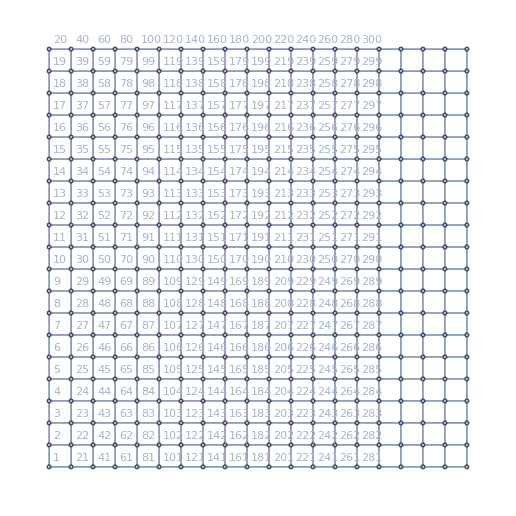

```mathematica
т=GridGraph[{20,20},VertexLabels->Automatic]
```

```mathematica
Do[If[Mod[i,20]≠0&&i≤400-20,т=EdgeAdd[т,i<->i+21]],{i,400}]
Do[If[i≤400-20&&Mod[i-1,20]≠0,т=EdgeAdd[т,i<->i+19]],{i,400}]
```

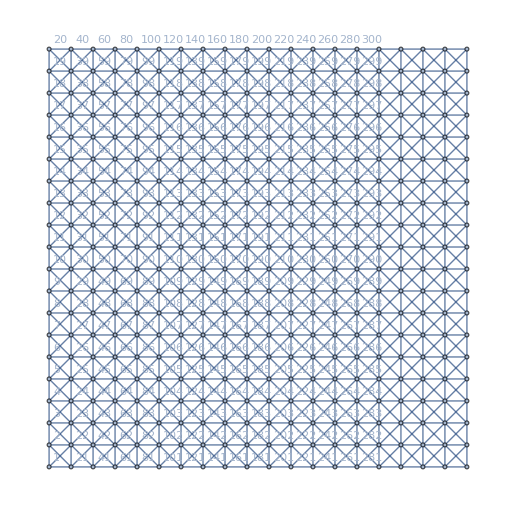

```mathematica
т
```

```mathematica
i=1
Dynamic[
Refresh[
i++,
UpdateInterval->3,
TrackedSymbols:>{}
]
]
```

```mathematica
oo=1
ooo=2
```

1

2

```mathematica
as={oo,ooo}
```

{1,2}

```mathematica
as={3,5}
```

{3,5}

```mathematica
{oo,ooo}={2,5}
```

{2,5}

```mathematica
oo
```

2

```mathematica
ooo
```

5

```mathematica
00
```

0

```mathematica
oo
```

1

```mathematica
DynamicModule[
{
px=100,
py=10,
pz=0,
viewd=0,
viewvector,
walls,
walledges,
fi,
checkbonds,
con1=1,
con2=1,
n=200,
wallcoords,
wal1,
gctoxyc,
botx=10,
boty=180,
botz=-10,
cutwalledges,
kudagolist={},
myshortestpath,
i
},
viewvector=Dynamic@{{px,py-1,pz},{px+viewd,py,pz}};
walls={
Gray,Cuboid[{100+21+1,100-100+1,-10},{100+1+19,100-60+1,10}],
Gray,Cuboid[{100+1+19,100-60+1,10},{100+1+40,100-62+1,-10}],
Gray,Cuboid[{100+1+38,100-62+1,-10},{100+1+40,100-22+1,10}],
Gray,Cuboid[{100+1+38,100-22+1,-10},{100+1+70,100-24+1,10}],
Gray,Cuboid[{100+1+70,100-22+1,10},{100+1+68,100-78+1,-10}],
Gray,Cuboid[{100+1+70,100-78+1,-10},{100+1+44,100-76+1,10}],
Gray,Cuboid[{100-60+1,100+0+1,-10},{100+1+40,100+2+1,10}],
Gray,Cuboid[{100-19+1,100-100+1,-10},{100-21+1,100-75+1,10}],
Gray,Cuboid[{100-19+1,100-77+1,10},{100-65+1,100-75+1,-10}],
Gray,Cuboid[{100-100+1,100-25+1,10},{100-55+1,100-27+1,-10}],
Gray,Cuboid[{100+45+1,100+100,10},{100+47+1,100+50+1,-10}],
Gray,Cuboid[{100+45+1,100+52+1,10},{100+65+1,100+50+1,-10}],
Gray,Cuboid[{100+65+1,100+68+1,10},{100+100,100+70+1,-10}],
Gray,Cuboid[{100-30+1,100+100,10},{100-32+1,100+40+1,-10}],
Gray,Cuboid[{100-30+1,100+40+1,10},{100-68+1,100+42+1,-10}],
Gray,Cuboid[{100-68+1,100+40+1,10},{100-66+1,100+70+1,-10}]
};

walledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]]
~Join~
{{199,∞},{1,200},{-∞,2},{1,200},{1,200},{199,∞},{1,200},{-∞,2}}
~Join~
{{100,100+5},{100,100+5}};

cutwalledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]];

gctoxyc[x_]:=If[Mod[x,200]==0,{Quotient[x,200],200},{Quotient[x,200]+1,Mod[x,200]}];

myshortestpath[px_,py_,botx_,boty_]:=Module[
{gcord,gcordbot},
gcord=(px-1)*200+py;
gcordbot=(botx-1)*200+boty;
kudagolist=FindShortestPath[gridg,gcord,gcordbot];
gctoxyc/@kudagolist
];

checkbonds[{x_,y_,z_}]:=Module[
{},
Total[
Table[
Boole[
If[
fi[x,y,walledges⟦i⟧,walledges⟦i+1⟧],
True,
False
]
],
{i,1,Length@walledges,2}
]
]
];

fi[x_,y_,xpat_,ypat_]:=Between[x,xpat]&&Between[y,ypat];
EventHandler[
Column[
{
Show[
Graphics3D[
walls
],
Graphics3D[
{Green,Dynamic@Cuboid[{px,py,10},{px+2,py+2,11}]}
],
Graphics3D[
{Red,Dynamic@Cuboid[{botx,boty,botz},{botx+5,boty+5,botz+15}],Red,Dynamic@Cuboid[{botx,boty,10},{botx+5,boty+5,11}]}
],
      ContourPlot3D[
{
z==-10,
z==10
},
{x,1,200},
{y,1,200},
{z,-10,10},
ContourStyle->
{
Texture[ExampleData[{"ColorTexture","Ash"}]],
Texture[ExampleData[{"ColorTexture","Ash"}]]
},
Mesh->False
],
 ContourPlot3D[
{
y==200,
y==1,
x==200,
x==1
},
{x,1,200},
{y,1,200},
{z,-10,10},
ContourStyle->
{
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]]
},
Mesh->False
]
],
i=1;
Dynamic@
Refresh[
If[
i≤Length@myshortestpath[botx,boty,px,py],
{botx,boty}=myshortestpath[botx,boty,px,py]⟦i++⟧,
i=1;{botx,boty}=myshortestpath[botx,boty,px,py]⟦i++⟧
],
TrackedSymbols:>{},
UpdateInterval->1
]
},
ItemStyle->White
],
DynamicUpdating->True,
{
"DownArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧-{0,2,0}]==0&&checkbonds[viewvector⟦1,1⟧-{0,2,0}]==0,py-=2]),
"UpArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧+{0,2,0}]==0&&checkbonds[viewvector⟦1,1⟧+{0,2,0}]==0,py+=2]),
"RightArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧+{2,0,0}]==0&&checkbonds[viewvector⟦1,1⟧+{2,0,0}]==0,px+=2]),
"LeftArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧-{2,0,0}]==0&&checkbonds[viewvector⟦1,1⟧-{2,0,0}]==0,px-=2]),
{"KeyDown","a"}:>(viewd-=2),
{"KeyDown","d"}:>(viewd+=2)
}
]
]
```